# Pendulum with variable length

## Theory

We assume the length of the pendulum to oscillate as l(t) = l_0+aCos(Ωt)
Hence the coordinates of the mass are P:( x = (l_0+aCos(Ωt))*sin(θ);  y = 0;  z = - (l_0+aCos(Ωt))*cos(θ) ) from which we can get 
Ṗ: ( ẋ=(l_0+a cos(Ωt))θ̇ cosθ-a Ωsin(Ωt)sinθ, OverDot[y=]0, ż=(l_0+a cos(Ωt))θ̇ sinθ+a Ωsin(Ωt)cosθ ) from which to find 
T = 1/2 m [(l(t))^2 (θ̇)^2+a^2 Ω^2 sin^2(Ωt)]	  and		U = -m g l(t) cos(θ) .
We can then determine the (simplified, since we will use it for the equation of motion) Lagrangian 
L = T - U = m[1/2 (l(t))^2 (θ̇)^2+1/2 a^2 Ω^2 sin^2(Ωt) +  g l(t) cos(θ) ] which for the equations of motion is the same as L = 1/2 (l(t))^2 (θ̇)^2 +  g l(t) cos(θ) .
Then ∂_(θ̇) L = l_t^2 θ̇    so   ∂_t (∂_(θ̇) L) = 2 l_t OverDot[l_t]θ̇+l_t^2 θ^(..) 	and 		∂_θ L = -g l_t sin(θ)
Finally we get the equations of motion  θ^(..)+ 2 OverDot[l(t)]/(l(t))θ̇ + g/(l(t))sin(θ)=0.
Up to rescaling the time and rewriting the coordinates in   ϕ(t)=θ(t/Ω)  ,   k = a/l_0   ,   α = ω/Ω  ,  ω=√(a/l_0) ,
 we get 		ϕ^(..) - (2k sin(t))/(1+ k cos(t))ϕ̇  +  α^2/(1+ k cos(t))sin(ϕ) = 0
of the Lagrange equation  L(q,q̇,t) =  1/2 (λ(t))^2(q̇)^2 + α^2 λ(t) cos(q)    where   λ(t)=1+k cos(t). Notice how since l(t)describes the length it must be positive, hence k<1.
The Legendre transformation is the time dependent diffeomorphism Λ_t:(q,q̇) →(q,p=∂_(q̇) L =λ(t)^2 q̇) . It’s periodic in time, and since we are studying the discrete dynamical system of the period shift map, the equations that describe it are actually Hamilton equations. Hence the Period Shift Map is volume preserving. 
Once again the fixed points (X=0) are z_+=(π,0) and z_-=(0,0).
The Poincarè Map is ψ : Σ_0 = M×{0} → Σ_0 that (z,0)→( PSM(z) = ϕ_(T,0)(z), 0) hence we can just study the Period Shift Map.
To study the stability we look to Spec(ψ ’(z_±) ) where the linearization can be solved using the variational equation U̇(t) = X’(z_±) U(t), U(0)=Id where
X’(θ,v) = (0 | 1
-α^2/(1+K cos(t))cos(θ) | (2K sin(t))/(1+K cos(t)))       hence, since they are fixed for the flow       X’(z_±) = (0 | 1
±α^2/(1+K cos(t)) | (2K sin(t))/(1+K cos(t)))  
Hence we can just solve, for the two linearizations, two differential equations of the form x^(..)=±α^2/(1+K cos(t))x+ (2K sin(t))/(1+K cos(t))ẋ with initial conditions (x(0),ẋ(0)) = (1,0) and (0,1).
If we denote with {λ_+,λ_-} the spectrum of the linearization of the P.M.  there are three cases (if both are real then since the product is +1 they are in either situation 1 or 3, and if they are complex they are complex conjugates and so in case 2) which can be distinguished using the trace of the matrix:
-Graphics-
Case 1 means z_± is Lyapunov-unstable and hyperbolic whereas cases 2 and 3 mean they are spectrally stable.
Let us find out, by varying the parameters α,K when they are unstable and spectrally stable.

## Functions

### Functions for the period shift map (or Poincaré Map)

```mathematica
X[{α_,k_}][{θ_,v_,t_}]:= {v,-α^2/(1+k Cos[t]) Sin[θ]  +2k   Sin[t]/(1+k Cos[t])v ,1}
mod[{θ_,v_,t_}]:={Mod[θ,2Pi,-Pi],v ,Mod[t,2Pi]}
Algo[αk_,h_][θvt_]:=mod[ θvt+h X[αk][θvt+h/2 X[αk][θvt]]  ]
Algo[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
Orb[θvt_,αk_,h_,T_]:=NestList[ Algo[αk,h],θvt,Floor[T/h]]
AlgoC= Compile[  {{αk,_Real,1},  h  ,  {xvt,_Real,1}  }  ,{Mod[xvt⟦1⟧+h (xvt⟦2⟧+(h (-αk⟦1⟧^2 Sin[xvt⟦1⟧]+2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+Cos[xvt⟦3⟧] αk⟦2⟧))),2 π,-π],xvt⟦2⟧+(h (-αk⟦1⟧^2 Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧]+2 αk⟦2⟧ (xvt⟦2⟧+(h (-αk⟦1⟧^2 Sin[xvt⟦1⟧]+2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧]))/(2 (1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧]))/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧),Mod[h+xvt⟦3⟧,2 π]}]
CompiledFunction[…]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{Mod[xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),2 π,-π],xvt⟦2⟧+h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),Mod[h+xvt⟦3⟧,2 π]}

CompiledFunction[…]

CompiledFunction[…]

```mathematica
OrbC[θvt_,αk_,h_,T_]:=NestList[ AlgoC[αk,h,#]&,θvt,Floor[T/h]]
```

```mathematica
PSMC=Compile[{{αk,_Real,1},{ndiv,_Integer},{θv,_Real,1} },
     Drop[ Nest[ AlgoC[ αk,  (2Pi)/ndiv ,#]&, Append[θv,0], ndiv] , - 1] ]
```

CompiledFunction[…]

```mathematica
OrbPSMC[θv_,nit_,αk_,ndiv_]:= NestList[PSMC[αk,ndiv,#]&,θv,nit]
```

Here too, allow the possibility of changing the PlotRange:

```mathematica
GOrbPSM[θv_,nit_,αk_,ndiv_,plrg_]:= ListPlot[ OrbPSMC[θv,nit,αk,ndiv], PlotRange->plrg,PlotStyle->PointSize[.009]]
```

### Functions to build the instability region

```mathematica
XL[{α_,k_}][{θ_,v_,t_}]:= {v,(-α^2/(1+k Cos[t]))  θ +((2k Sin[t])/(1+k Cos[t]))v ,1}
```

```mathematica
AlgoL[αk_,h_][θvt_]:=θvt+h XL[αk][θvt+h/2 XL[αk][θvt]] 
OrbL[θvt_,αk_,h_,T_]:=NestList[ AlgoL[αk,h],θvt,Floor[T/h]]
```

```mathematica
AlgoL[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-((xvt⟦1⟧+1/2 h xvt⟦2⟧) αk⟦1⟧^2)/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}

```mathematica
AlgoLC=Compile[{{αk,_Real,1},h,{xvt,_Real,1}},{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-((xvt⟦1⟧+1/2 h xvt⟦2⟧) αk⟦1⟧^2)/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}];
```

```mathematica
SolEqVar=Compile[
{{αk,_Real,1},ndiv,{xv,_Real,1}},
Take[     Nest[AlgoLC[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv]   , 2]
];
```

```mathematica
LinPSM[ ak_ , ndiv_]:={  SolEqVar[ak,ndiv,{1,0}]  ,  SolEqVar[ak,ndiv,{0,1}]  }
```

```mathematica
TrLin[αk_,ndiv_]:=Abs[Tr[LinPSM[αk,ndiv]]]
```

```mathematica
αkTrLin[{a_,k_} ,ndiv_]:= { a , k, TrLin[{a,k},ndiv] }
```

```mathematica
sel[lst_]:=Select[lst,#[[-1]]>2&]
```

```mathematica
Sez[lst_]:=Map[Drop[#,-1]&,sel[lst]]
```

```mathematica
RandTrLin[npts_,ndiv_,αint_, kint_]:=ParallelTable[αkTrLin[{RandomReal[αint],RandomReal[kint]},ndiv],npts]
```

```mathematica
InstaReg[lst_,αint_, kint_]:=ListPlot[(Drop[#1,-1]&)/@sel[lst],PlotRange->{αint,kint},PlotStyle->PointSize[0.005]]
```

### Functions for the animation of the pendulum

```mathematica
l[l0_,α_,k_][t_]:=l0+k l0 Cos[(Sqrt[k]/α)t]
```

```mathematica
pen[l0_,α_,k_][{θ_,v_,t_}]:={{0,0},{l[l0,α,k][t]Sin[θ],-l[l0,α,k][t]Cos[θ]}} ;
gpen[l0_,α_,k_][xvt_]:=Show[   Graphics[ {Thickness[.03], Line[  pen[l0,α,k][xvt] ]}  ]   ,PlotRange->{{-2,2},{-2,2}} ,  Axes->True,Ticks->None  ] ;
motion[{x_,v_},{l0_,α_,k_},{h_,T_},r_]:=Module[{mgpen},
  mgpen= Map[  gpen[l0,α,k], Orb[{x,v,0},{α,k},h,T]]; 
  Animate[mgpen[[n]] ,{n,1,Length[mgpen],1}, AnimationRate->r]]
```

## Analysis of the instability tongues

```mathematica
{regx,regy} = {{0,2},{0,1}};
```

```mathematica
pts=RandTrLin[20000,400,regx,regy];
```

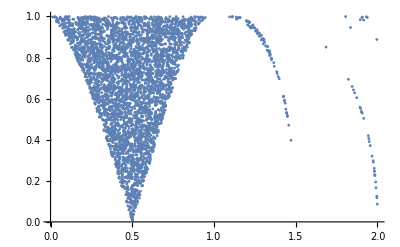

```mathematica
InstaReg[pts,regx,regy]
```

For k=0 the equations that determine the trace of the linearization become x^(..)=-(2K sin(t))/(1+K cos(t))ẋ with initial conditions (x(0),ẋ(0)) = (1,0) and (0,1) Although I have not been able to compute the solution analitically we can verify numerically that once again there are contact points at every 
 α=m/2 for m∈Z. These are the contact points of the cusps on the α axis.

The instability region appears to be composed of several different tongues. How many are they? Where are they?  Let us plot  the absolute value of the trace of the linearization on the line k =00.1 and highlight in red when it goes above 2.

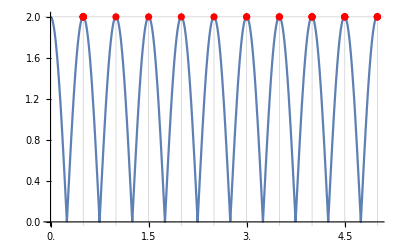

```mathematica
k=0.01;
line = Map[{#,k}&,Range[0,5,0.001]];
selected =Map[Drop[#,-1]&,sel[Map[αkTrLin[#,1000]&,line]]];
selected=Map[#+{0,2-k}&,selected];
Show[Plot[TrLin[{α,k},400],{α,0,5},GridLines->{Range[0,5,0.5],{2}},Ticks->{Range[0,5,0.5],Automatic}],ListPlot[selected,PlotStyle-> Red]]
```

Each red segment corresponds to values of α such that (α,k=0.01) belongs to an instability region. We can see that we have separate ‘pieces’ of instability regions corresponding to each half integer. This hints towards the existence of infinitely many tongues, one for every half integer.

### First tongue

Let us zoom in on the first tongue.

```mathematica
pts = Union[pts,RandTrLin[10000,400,{0.3,0.7},{0,0.65}]  ];
```

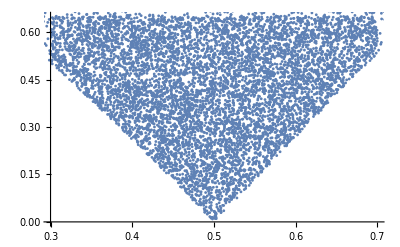

```mathematica
InstaReg[ pts,{0.3,0.7},{0,0.65}  ]
```

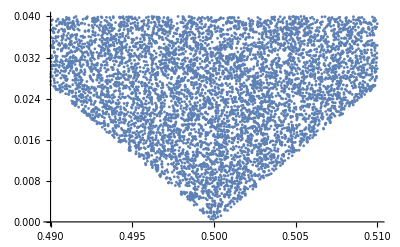

```mathematica
pts = Union[pts,RandTrLin[10000,400,{0.49,0.51},{0,0.04}]  ];
InstaReg[ pts,{0.49,0.51},{0,0.04}  ]
```

Similarly to the case of the pendulum with oscillating support this is not a cusp, but has a nonzero angle at its tip.
Hence for small values of k, its more probable that the lower equilibrium is unstable for Ω close to 2ω.

### Behaviour near the first tongue

Let us some phase portrait for parameter values, outside, inside and at the exit of the first instability tongue.

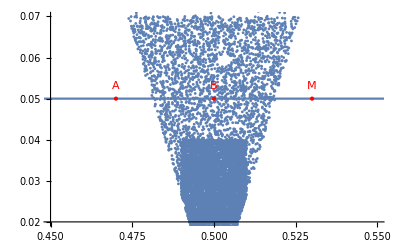

```mathematica
pts = Union[pts,RandTrLin[10000,400,{.45,.55},{.02,.07}]  ];
A={.47,.05};
B={.5,.05};
M={.53,.05};
Show[InstaReg[pts,{.45,.55},{.02,.07}],Plot[.05,{x,.4,.6}],Graphics[{PointSize[Large],Red,Text["A",A+{0,0.003}],Point[A],Text["B",B+{0,0.003}], Point[B] ,Text["M",M+{0,0.003}], Point[M] }]]
```

Point A

```mathematica
gorbA0 = GOrbPSM[ {0, 0.001} , 500 , A , 400 , {{-0.52,.52}, {-.12,.12}} ];
gorbA1 = GOrbPSM[ {0, 0.02} , 500 , A , 400 , {{-0.5,.5}, {-.5,.5}} ];
gorbA2 = GOrbPSM[ {0, 0.05} , 500 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA3 = GOrbPSM[ {0, 0.1} , 1000 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbA4 = GOrbPSM[ {0,-0.2} , 1000 , A , 400 , {{-0.5,.5}, {-.5,.5} } ];
```

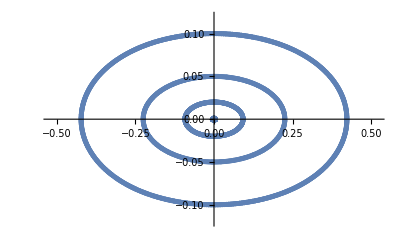

```mathematica
Show[ gorbA0,gorbA1,gorbA2,gorbA3,gorbA4]
```

Point B

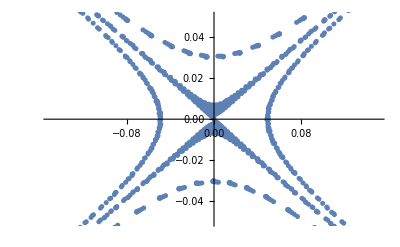

```mathematica
gorbB0 = GOrbPSM[ {0, 0.001} , 1000 , B , 200 , {{-0.15,.15}, {-.05,.05}} ];
gorbB1 = GOrbPSM[ {0.05, 0} , 500 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbB2 = GOrbPSM[ {0, -0.03} , 500 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
gorbB3 = GOrbPSM[ {0, 0.1} , 1000 , B , 200 , {{-0.5,.5}, {-.5,.5} } ];
Show[ gorbB0,gorbB1,gorbB2,gorbB3]
```

Point C

```mathematica
gorbM0 = GOrbPSM[ {0, 0.001} , 500 , M , 400 , {{-0.22,.22}, {-.22,.22}} ];
gorbM1 = GOrbPSM[ {0, 0.02} , 500 , M , 400 , {{-0.5,.5}, {-.5,.5}} ];
gorbM2 = GOrbPSM[ {0, 0.05} , 500 , M , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbM3 = GOrbPSM[ {0, 0.1} , 1000 , M , 400 , {{-0.5,.5}, {-.5,.5} } ];
gorbM4 = GOrbPSM[ {0,-0.2} , 1000 , M , 400 , {{-0.5,.5}, {-.5,.5} } ];
```

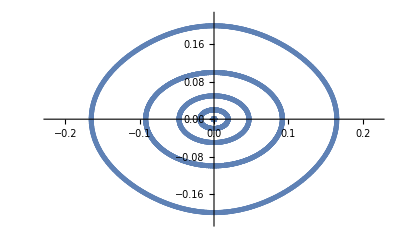

```mathematica
Show[ gorbM0,gorbM1,gorbM2,gorbM3,gorbM4]
```

We can see pretty clearly the change of the lower equilibrium from elliptic (stable), to hyperbolic (unstable)back to elliptic again.

Finally, for a point P outside the tongue, let us simulate the unstable behaviour of the pendulum:

```mathematica
P={.8,.575};
```

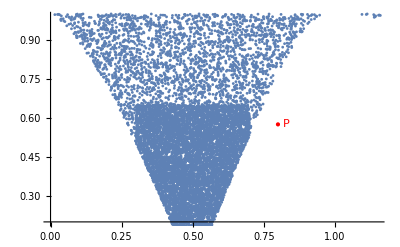

```mathematica
Show[InstaReg[pts,{0,1.15},{0.2,0.99} ],Graphics[{PointSize[Medium],Red,Text["P",P+{0.03,0}],Point[P]}]]
```

```mathematica
mgpen= Map[  gpen[1,0.8,0.57], Orb[Append[P,0],{0.8,0.57},0.01,500]];
```

```mathematica
Animate[mgpen[[n]] ,{n,1,Length[mgpen],1}, AnimationRate->100]
```